```mathematica
num=Table[i,{i,14}];
comb2=Subsets[num,{2}];
array=Join[comb2,Table[{15,15},5]];
array1=Flatten[Table[{array[[i]],array[[i]],array[[i]]},{i,Length@array}],1];
member=IntegerDigits[array,2,4];
Redun=Total[member,{2}];
Position[array,{7,8}]
```

{{64}}

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
Data=ToExpression@Import[FileNameJoin[{NotebookDirectory[],"2coculture-new.xlsx"}]];
Data=Transpose@Table[Flatten@Transpose[Transpose[Data[[i]]][[1;;12]]],{i,Length@Data}];
Data=(Data-0.05)*2;
time=Table[6+12*i,{i,0,12}];
time=Join[{0},time];
growthadthrouhold=2.5;
parameters={};
Do[
data={time,Data[[i]]};
model=A2+(A1-A2)/(1+Exp[(t-x0)/dx]);
logfit=NonlinearModelFit[Transpose@data,model,{A2,A1,x0,dx},t];
Rsquare=logfit["AdjustedRSquared"];
Pvalue=logfit["ParameterPValues"];
eqn=logfit["BestFit"];
Xmax=A2/.logfit["BestFitParameters"];
Xmax1=Max[Take[Data[[i]],{3,-1}]];
X0=A1/.logfit["BestFitParameters"];
X01=Data[[i,1]];
foldgrowth=Xmax1/X01;
foldgrowth1=Xmax/X0;
fasttp=x0/.logfit["BestFitParameters"];
Mumax=logfit'[fasttp];
lagtime=t/.Flatten@Solve[Mumax(t-fasttp)+((Xmax+X0)/2)==X01,t];
lagtimere=100-lagtime;
growthad=If[foldgrowth>growthadthrouhold,true,false];
parameters=Join[parameters,{Join[array1[[i]],{lagtime,lagtimere,Mumax,fasttp,Xmax1,X01,foldgrowth,foldgrowth1,Rsquare,growthad}]}];
,{i,1,Length@Data}];
parameters=Join[{{"member1","member2","lagtime","lagtimere","Mumax","fasttp","Xmax","X0","foldgrowth","foldgrowth1","Rsquare","growthad"}},parameters];
Export[FileNameJoin[{NotebookDirectory[],"2co-growparameters.xlsx"}],parameters];
```

General::munfl: Exp[-5490.92] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-4023.34] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1088.19] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of NonlinearModelFit::cvmit will be suppressed during this calculation.

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit::sszero will be suppressed during this calculation.

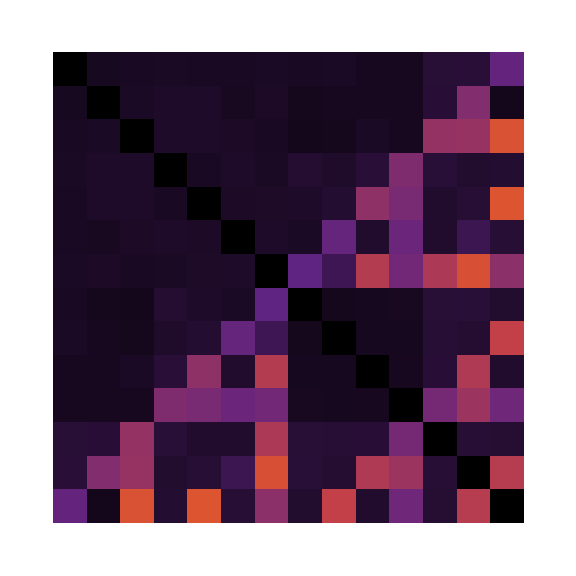

```mathematica
SetDirectory[FileNameJoin[{NotebookDirectory[]}]];
para=Take[Import[FileNameJoin[{NotebookDirectory[],"2co-growparameters.xlsx"}],{"Data",1}],{2,-1}];
ID=array;
lagtimecat=Partition[Flatten[Take[para,All,{4}]],3];
Mumaxcat=Partition[Flatten[Take[para,All,{5}]],3];
foldgrowthcat=Partition[Flatten[Take[para,All,{9}]],3];
lagtimemean=Mean[Transpose@lagtimecat];
lagtimeDev=StandardDeviation[Transpose@lagtimecat];
Mumaxmean=Mean[Transpose@Mumaxcat];
MumaxDev=StandardDeviation[Transpose@Mumaxcat];
foldgrowthmean=Mean[Transpose@foldgrowthcat];
foldgrowthDev=StandardDeviation[Transpose@foldgrowthcat];
lagtimeplotdata=Table[0,{16},{16}];
baseplot=Partition[Table[ColorData["SunsetColors"][0],196],14];
plotdata=Transpose@Join[Transpose@ID,{lagtimemean},{Mumaxmean},{foldgrowthmean}];
foldgrowthplotlist={};
Mumaxplotlist={};
lagtimeplotlist={};
num=Table[i,{i,14}];
foldgrowthsub=baseplot;
Mumaxsub=baseplot;
lagtimesub=baseplot;
Do[
datasub2=plotdata[[j]];
subID=datasub2[[1;;2]];
foldgrowthsub=ReplacePart[foldgrowthsub,{subID->ColorData["SunsetColors"][datasub2[[5]]/30],Reverse@subID->ColorData["SunsetColors"][datasub2[[5]]/30]}];
Mumaxsub=ReplacePart[Mumaxsub,{subID->ColorData["SunsetColors"][datasub2[[4]]/1],Reverse@subID->ColorData["SunsetColors"][datasub2[[4]]/1]}];
lagtimesub=ReplacePart[lagtimesub,{subID->ColorData["SunsetColors"][datasub2[[3]]/100],Reverse@subID->ColorData["SunsetColors"][datasub2[[3]]/100]}];
,{j,Length@plotdata}];
foldgrowthplot=MatrixPlot[foldgrowthsub,AspectRatio->1,ImageSize->Large,Frame->False]
Mumaxplot=MatrixPlot[Mumaxsub,AspectRatio->1,ImageSize->Large,Frame->False];
lagtimeplot=MatrixPlot[lagtimesub,AspectRatio->1,ImageSize->Large,Frame->False];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"plot","foldgrowthplot.tif"}],foldgrowthplot];
Export[FileNameJoin[{NotebookDirectory[],"plot","Mumaxgridplot.tif"}],Mumaxplot];
Export[FileNameJoin[{NotebookDirectory[],"plot","lagtimegridplot.tif"}],lagtimeplot];
ColorData["SunsetColors","Image"];
```

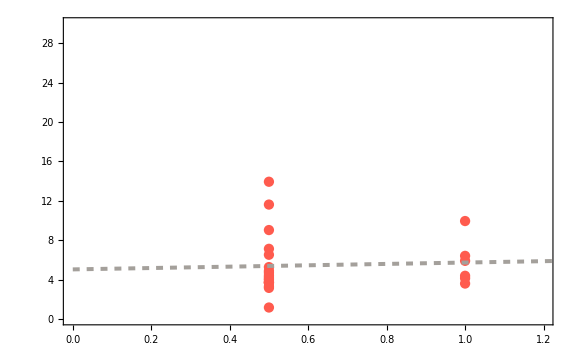

```mathematica
Redundata=Redun;
fitdata=Transpose@Join[Transpose@Redundata,Transpose@Take[plotdata,All,{3,5}]];
fiterrordata=Transpose@Join[Transpose@Redundata,Join[{lagtimeDev},{MumaxDev},{foldgrowthDev}]];
fitdata2=Select[fitdata,MemberQ[#,0]==False&];

Redundata1=Transpose@Join[{Flatten@Take[fitdata2,All,{1}]/2},{Flatten@Take[fitdata2,All,{7}]}];
fit1=LinearModelFit[Redundata1,x,x];
fit1["ParameterPValues"];
R1quare=fit1["AdjustedRSquared"];
Redun1plot=Show[ListPlot[Redundata1,PlotStyle->{RGBColor[1,91/255,78/255]},Frame->True,PlotRange->{{0,1.2},{0,30}},FrameTicksStyle->Directive[Black,20],FrameStyle->Thick,ImageSize->Large],Plot[fit1[x],{x,0,4},PlotStyle->{Dashed,Thickness[0.005],RGBColor[164/255,160/255,155/255]},ImageSize->Large]]

Redundata2=Transpose@Join[{Flatten@Take[fitdata2,All,{2}]/2},{Flatten@Take[fitdata2,All,{7}]}];
fit2=LinearModelFit[Redundata2,x,x];
fit2["ParameterPValues"];
R2quare=fit2["AdjustedRSquared"];
Redun2plot=Show[ListPlot[Redundata2,PlotStyle->{RGBColor[1,91/255,78/255]},Frame->True,PlotRange->{{0,1.2},{0,30}},FrameTicksStyle->Directive[Black,20],FrameStyle->Thick,ImageSize->Large],Plot[fit2[x],{x,0,4},PlotStyle->{Dashed,Thickness[0.005],RGBColor[164/255,160/255,155/255]},ImageSize->Large]];

Redundata3=Transpose@Join[{Flatten@Take[fitdata2,All,{3}]/2},{Flatten@Take[fitdata2,All,{7}]}];
fit3=LinearModelFit[Redundata3,x,x];
fit3["ParameterPValues"];
R3quare=fit3["AdjustedRSquared"];
Redun3plot=Show[ListPlot[Redundata3,PlotStyle->{RGBColor[1,91/255,78/255]},Frame->True,PlotRange->{{0,1.2},{0,30}},FrameTicksStyle->Directive[Black,20],FrameStyle->Thick,ImageSize->Large],Plot[fit3[x],{x,0,4},PlotStyle->{Dashed,Thickness[0.005],RGBColor[164/255,160/255,155/255]},ImageSize->Large]];

Redundata4=Transpose@Join[{Flatten@Take[fitdata2,All,{4}]/2},{Flatten@Take[fitdata2,All,{7}]}];
fit4=LinearModelFit[Redundata4,x,x];
fit4["ParameterPValues"];
R4quare=fit4["AdjustedRSquared"];
Redun4plot=Show[ListPlot[Redundata4,PlotStyle->{RGBColor[1,91/255,78/255]},Frame->True,PlotRange->{{0,1.2},{0,30}},FrameTicksStyle->Directive[Black,20],FrameStyle->Thick,ImageSize->Large],Plot[fit4[x],{x,0,4},PlotStyle->{Dashed,Thickness[0.005],RGBColor[164/255,160/255,155/255]},ImageSize->Large]];
Export[FileNameJoin[{NotebookDirectory[],"plot","redun1.tif"}],Redun1plot];
Export[FileNameJoin[{NotebookDirectory[],"plot","redun2.tif"}],Redun2plot];
Export[FileNameJoin[{NotebookDirectory[],"plot","redun3.tif"}],Redun3plot];
Export[FileNameJoin[{NotebookDirectory[],"plot","redun4.tif"}],Redun4plot];
```

```mathematica
plotdata;
Export[FileNameJoin[{NotebookDirectory[],"2co-growparameters-average.xlsx"}],plotdata];
```

```mathematica
phenotypelist=Tuples[{0,1},4];
phenotypelist1=DeleteCases[DeleteCases[phenotypelist,{1,1,1,1}],{0,0,0,0}];
comb=Subsets[phenotypelist,{2}];
combre=Table[Total[Transpose[comb[[i]]][[j]]],{i,1,Length@comb},{j,1,4}];
comb1=Select[comb,Product[Total[Transpose[#][[i]]],{i,1,4}]!=0&];
comb1re=Table[Total[Transpose[comb1[[i]]][[j]]],{i,1,Length@comb1},{j,1,4}];
matrix={};
Do[
Do[
ecomb={phenotypelist[[j]],phenotypelist[[i]]};
elem=If[Product[Total[Transpose[ecomb][[i]]],{i,1,4}]==0,0,1];
matrix=Join[matrix,{elem}];
,{j,Length@phenotypelist}];
,{i,Length@phenotypelist}];
Count[matrix,1];
matrix=Partition[matrix,16];
plot=ArrayPlot[matrix,PlotLegends->Automatic,FrameTicks->All,ColorFunction->"BlueGreenYellow",ColorFunctionScaling->False,AspectRatio->1,ImageSize->Large,Mesh->All,MeshStyle->{{Gray, Thick},{Gray,Thick}}]
```